```mathematica
FullSimplify[({{Cos[ω[x,y]], -Sin[ω[x,y]]}, {Sin[ω[x,y]], Cos[ω[x,y]]}})ᵀ.({{λ1[x,y], 0}, {0, λ2[x,y]}}).({{Cos[ω[x,y]], -Sin[ω[x,y]]}, {Sin[ω[x,y]], Cos[ω[x,y]]}})]
```

{{Cos[ω[x,y]]^2 λ1[x,y]+Sin[ω[x,y]]^2 λ2[x,y],Cos[ω[x,y]] Sin[ω[x,y]] (-λ1[x,y]+λ2[x,y])},{Cos[ω[x,y]] Sin[ω[x,y]] (-λ1[x,y]+λ2[x,y]),Sin[ω[x,y]]^2 λ1[x,y]+Cos[ω[x,y]]^2 λ2[x,y]}}

```mathematica
FullSimplify[Eigensystem[{{Cos[ω[x,y]]^2 λ1[x,y]+Sin[ω[x,y]]^2 λ2[x,y],Cos[ω[x,y]] Sin[ω[x,y]] (-λ1[x,y]+λ2[x,y])},{Cos[ω[x,y]] Sin[ω[x,y]] (-λ1[x,y]+λ2[x,y]),Sin[ω[x,y]]^2 λ1[x,y]+Cos[ω[x,y]]^2 λ2[x,y]}}]]
```

{{λ1[x,y],λ2[x,y]},{{-Cot[ω[x,y]],1},{Tan[ω[x,y]],1}}}

```mathematica
T11[x_,y_]:=Cos[ω[x,y]]^2 λ1[x,y]+Sin[ω[x,y]]^2 λ2[x,y]
T12[x_,y_]:=Cos[ω[x,y]] Sin[ω[x,y]] (-λ1[x,y]+λ2[x,y])
T22[x_,y_]:=Sin[ω[x,y]]^2 λ1[x,y]+Cos[ω[x,y]]^2 λ2[x,y]
```

```mathematica
sol=FullSimplify[Solve[
{t11==Cos[ω]^2 λ1+Sin[ω]^2 λ2,
t12==Cos[ω] Sin[ω] (-λ1+λ2),
t22==Sin[ω]^2 λ1+Cos[ω]^2 λ2},{λ1,λ2,ω}],Assumptions->{t11>t22,t12∈Reals,0<ω<π}]
```

{{λ1→1/2 (t11+√(4 t12^2+(t11-t22)^2)+t22),λ2→1/2 (t11-√(4 t12^2+(t11-t22)^2)+t22),ω→ConditionalExpression[ArcTan[-2,(-t11+√(4 t12^2+(t11-t22)^2)+t22)/t12]+2 π C[1], C[1]∈ℤ]},{λ1→1/2 (t11+√(4 t12^2+(t11-t22)^2)+t22),λ2→1/2 (t11-√(4 t12^2+(t11-t22)^2)+t22),ω→ConditionalExpression[-ArcCot[(2 t12)/(-t11+√(4 t12^2+(t11-t22)^2)+t22)]+2 π C[1], C[1]∈ℤ]},{λ1→1/2 (t11-√(4 t12^2+(t11-t22)^2)+t22),λ2→1/2 (t11+√(4 t12^2+(t11-t22)^2)+t22),ω→ConditionalExpression[ArcTan[t11-√(4 t12^2+(t11-t22)^2)-t22,-2 t12]+2 π C[1], C[1]∈ℤ]},{λ1→1/2 (t11-√(4 t12^2+(t11-t22)^2)+t22),λ2→1/2 (t11+√(4 t12^2+(t11-t22)^2)+t22),ω→ConditionalExpression[ArcTan[-t11+√(4 t12^2+(t11-t22)^2)+t22,2 t12]+2 π C[1], C[1]∈ℤ]}}

```mathematica
sol1=FullSimplify[{λ1,λ2,Sin[ω],Cos[ω]}/.sol⟦2⟧/.C[1]->0,Assumptions->{t11>t22,t12∈Reals}]
```

{1/2 (t11+√(4 t12^2+(t11-t22)^2)+t22),1/2 (t11-√(4 t12^2+(t11-t22)^2)+t22),-(-t11+√(4 t12^2+(t11-t22)^2)+t22)/(2 t12 √(1+((-t11+√(4 t12^2+(t11-t22)^2)+t22)^2)/(4 t12^2))),1/(√(1+((-t11+√(4 t12^2+(t11-t22)^2)+t22)^2)/(4 t12^2)))}

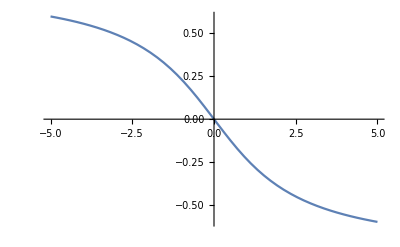

```mathematica
Block[{t11=4,t22=0.},Plot[Evaluate[ω/.sol/.C[1]->0]⟦2⟧,{t12,-5,5},PlotLegends->Automatic]]
```

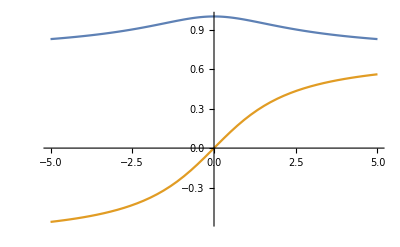

```mathematica
Block[{t11=4,t22=0},
Plot[{ Cos[Evaluate[ω/.sol/.C[1]->0]⟦2⟧],-Sin[Evaluate[ω/.sol/.C[1]->0]⟦2⟧]},{t12,-5,5}]
]
```

```mathematica
Limit[{ Cos[Evaluate[ω/.sol/.C[1]->0]⟦2⟧],-Sin[Evaluate[ω/.sol/.C[1]->0]⟦2⟧]},t12->0,Assumptions->{t11>t22}]
```

{1,0}

```mathematica
Limit[D[{ Cos[Evaluate[ω/.sol/.C[1]->0]⟦2⟧],-Sin[Evaluate[ω/.sol/.C[1]->0]⟦2⟧]},t12],t12->0,Assumptions->{t11>t22}]
```

{0,1/(t11-t22)}

```mathematica
v1={ Cos[Evaluate[ω/.sol/.C[1]->0]⟦2⟧],-Sin[Evaluate[ω/.sol/.C[1]->0]⟦2⟧]}
```

{1/(√(1+((-t11+√(4 t12^2+(t11-t22)^2)+t22)^2)/(4 t12^2))),(-t11+√(4 t12^2+(t11-t22)^2)+t22)/(2 t12 √(1+((-t11+√(4 t12^2+(t11-t22)^2)+t22)^2)/(4 t12^2)))}